```mathematica
Subscript[H, 0]=3;
Subscript[S, 0]=1;
Subscript[S, 01]=0.7;
Subscript[S, 02]=0.3;
α=2.4;
A13=K^2*Subscript[H, 0]*1/16*(1/Subscript[H, 0]^2-K^2)*((4.0*Subscript[H, 0]^2*Log[Subscript[H, 0]/(1+Subscript[S, 0])])-(3.0*Subscript[H, 0]^2)+(4.0*(1+Subscript[S, 0])*(1+Subscript[S, 0]))-(1+Subscript[S, 0])^4/Subscript[H, 0]^2);
A14=1/(1-(((1+Subscript[S, 0])*Subscript[S, 0]*α)/(Subscript[H, 0]-α)*(1/Subscript[H, 0]^2-K^2)));


p1=Plot[{{(1/(1-(((1+Subscript[S, 0])*Subscript[S, 0]*α)/(Subscript[H, 0]-α)*(1/Subscript[H, 0]^2-K^2))))*K^2*Subscript[H, 0]*1/16*(1/Subscript[H, 0]^2-K^2)*((4.0*Subscript[H, 0]^2*Log[Subscript[H, 0]/(1+Subscript[S, 0])])-(3.0*Subscript[H, 0]^2)+(4.0*(1+Subscript[S, 0])*(1+Subscript[S, 0]))-(1+Subscript[S, 0])^4/Subscript[H, 0]^2)},{(1/(1-(((1+Subscript[S, 01])*Subscript[S, 01]*α)/(Subscript[H, 0]-α)*(1/Subscript[H, 0]^2-K^2))))*K^2*Subscript[H, 0]*1/16*(1/Subscript[H, 0]^2-K^2)*((4.0*Subscript[H, 0]^2*Log[Subscript[H, 0]/(1+Subscript[S, 01])])-(3.0*Subscript[H, 0]^2)+(4.0*(1+Subscript[S, 01])*(1+Subscript[S, 01]))-(1+Subscript[S, 01])^4/Subscript[H, 0]^2)},{(1/(1-(((1+Subscript[S, 02])*Subscript[S, 02]*α)/(Subscript[H, 0]-α)*(1/Subscript[H, 0]^2-K^2))))*K^2*Subscript[H, 0]*1/16*(1/Subscript[H, 0]^2-K^2)*((4.0*Subscript[H, 0]^2*Log[Subscript[H, 0]/(1+Subscript[S, 02])])-(3.0*Subscript[H, 0]^2)+(4.0*(1+Subscript[S, 02])*(1+Subscript[S, 02]))-(1+Subscript[S, 02])^4/Subscript[H, 0]^2)}},{K,0,0.4},
Frame->True,FrameLabel->{{HoldForm["Σ"],None},{HoldForm[K],None}},FrameStyle->Directive[Bold,Black,(FontSize->14)], PlotStyle->{Red,Directive[Dashed,Green],Directive[Dotted,Blue]},AxesStyle->AbsoluteThickness[5],PlotLegends->Placed[LineLegend[{"S_0=1","S_0=0.7","S_0=2.4"},LegendLayout->{"Column",1},LegendMarkerSize->14],{Left,0.9},Pane[#,450,Alignment->Left]&],PlotRange->{All,{0.0000001,0.007}}]
```

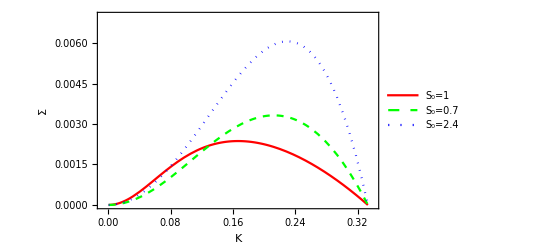

```mathematica
SystemOpen["exportP1.pdf"]
```

```mathematica
SystemOpen["exportP1.pdf"]
```

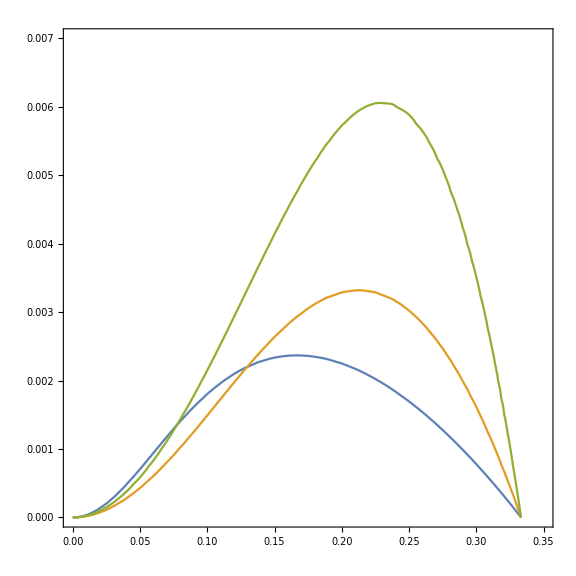

```mathematica
Show[%52,ImageSize->Large]
```

```mathematica
Show[%54,FrameLabel->{{RawBoxes[RowBox[{"Σ",RowBox[{"(",RowBox[{"α",",","K"}],")"}]}]],None},{HoldForm[K],None}},PlotLabel->None,LabelStyle->{18,GrayLevel[0],Bold}]
```

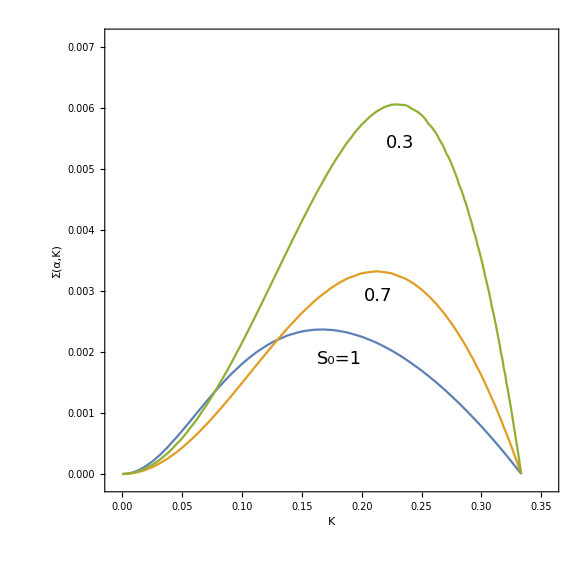

```mathematica
Show[%52,ImageSize->Large]
```